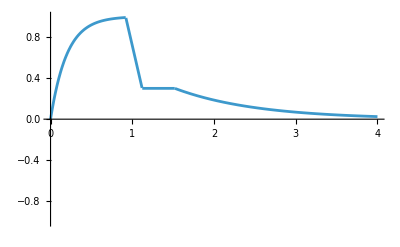

```mathematica
synth[attackvalue_:5,sustain_:0.3,tempsdecayenplus_:0.2,tempssustainenplus_:0.4]:=
Module[{a,d,s,r},
a=attaque[t_]:=1-Exp[-attackvalue t];
tempsA=Solve[attaque[t]==99/100,t∈Reals][[1,1,2]];
    tempsD=tempsA+tempsdecayenplus;
d=decay[t_]:=((sustain-attaque[tempsA])/(tempsD-tempsA)) t+(attaque[tempsA]-(sustain-attaque[tempsA])/(tempsD-tempsA)*tempsA);
tempsS=tempssustainenplus+tempsD;
s=sustain;
r=release[t_]:=sustain*Exp[tempsS-t];
ADSR[t_]:=Piecewise[{{attaque[t],t<=tempsA},{decay[t],tempsA<t<=tempsD},{sustain,tempsD<t<=tempsS},{release[t],tempsS<=t}}];Plot[ADSR[t],{t,0,4},PlotRange->{All,{-1,1}}]
]
(*enter the ADSR parameters in the synth fct or juste leave the default values*)
synth[(*we put the default settings*)];

f=100;
f0=300;
f1=200;
sinuso[t_]:=Sin[2Pi f t]+.5 Sin[4Pi f t]+.1 Sin[Pi f t];
triangle[t_]:=2Pi ArcSin[Sin[2Pi f t]];
bruit[t_]:=RandomReal[{0,1}];
carre[t_]:=Sign[Sin[2Pi f t]];
FM[t_]:=Sin[2 Pi (f0 t+(f1/f) (1-Cos[2 Pi f t]))];
AM[t_]:=(1+Sin[2Pi t f1]) Sin[2Pi t f0]
pitch[p_]:=AudioPitchShift[yc,p]
reverb[sound_]:=AudioReverb[sound]
reverse[sound_]:=AudioReverse[sound]

synth[(*values*)]
Fonction[t_]:=ADSR[t]*carre[t]




HP[signal_,fc_]:=HighpassFilter[signal,fc,44100]
LP[signal_,fc_]:=LowpassFilter[signal,fc,44100]
```

# Fourier

```mathematica
FT[audio_,nPeaks_:5]:=Module[{audioObj,fs,data,len,fft,mag,phase,indices,freqValues,maxAmp,terms,i},Quiet@Check[audioObj=If[Head[audio]===Sound,Audio[audio],audio];
fs=AudioSampleRate[audioObj];
data=Flatten[AudioData[audioObj]];
len=Length[data];
If[len==0||Max[Abs[data]]<10^-6,Return[<|"Equation"->"0","Frequencies"->{0},"Status"->"Silent"|>];];
fft=Fourier[data,FourierParameters->{1,-1}];
mag=Abs[fft][[;;Ceiling[len/2]]];
phase=Arg[fft][[;;Ceiling[len/2]]];
indices=If[Length[mag]>=nPeaks,Ordering[mag,-nPeaks],Range[Length[mag]]];
freqValues=QuantityMagnitude[N[(indices-1)*fs/len]];
freqValues=Select[freqValues,20<=#<=20000&];
If[freqValues=={},Return[<|"Error, no signal detected"|>]];
maxAmp=If[Length[mag[[indices]]]>0,Max[mag[[indices]]],Return["Erreur, pas de signal"]];terms=Table[With[{a=Round[mag[[indices[[i]]]]/maxAmp,0.01],f=Round[freqValues[[i]],0.1],ϕ=Round[phase[[indices[[i]]]],0.1]},ToString[a]<>" Sin[2π×"<>ToString[f]<>"×t + "<>ToString[ϕ]<>"]"],{i,Min[nPeaks,Length[freqValues]]}];
<|"Equation"->StringJoin[Riffle[terms," + "]],"Frequencies"->freqValues,"Amplitudes"->mag[[indices]]/maxAmp,"Phases"->phase[[indices]],"Status"->"Success!!!"|>,<|"Status"->"Error","Message"->"Analysis failed"|>]]
```

# Presets

```mathematica
(*Finally,we added presets:*)
(*Kick:*)
(*attackvalue = 5000*)
(*sustain = 0.3*)
(*tempsdecayenplus = 0.01*)
(*tempssustainenplus = 0.01*)
(*f=100,the sound lasts very short we use square*)
(*Piano (C):*)
(*attackvalue = 100*)
(*sustain = 0.7*)
(*tempsdecayenplus = 0.05*)
(*tempssustainenplus = 0.5*)
(*the sound lasts 4s,we use the FT function,add the ADSR envelope,and add a little background noise (very soft,multiplied by 1/20) if necessary*)
(*Hi-Hats:*)
(*attackvalue = 5000*)
(*sustain = 0.2*)
(*tempsdecayenplus = 0.02*)
(*tempssustainenplus = 0.05*)
(*f=180,f0=4000,f1=3000, The sound lasts very short,0.3 seconds.We use noise,square,and AM in addition,with the envelope,and we must use the High-Pass,with fc=8000.*)
(*Snare:*)
(*Kick parameters*)
(*the only difference is that we also use noise *)(*(noise for the muffled side of the snare*)(*and square for the punchy side)*)
(*Organ:*)
(*Same parameters as the piano for the ADSR.*)
(*We use FT (FT*ADSR) and divide the total by 2*)(*to avoid saturation.*)
(*Since the synth is home-made,the presets do sound like a kitchen recipe,but we couldn't really do better than this…*)
```

# Sound

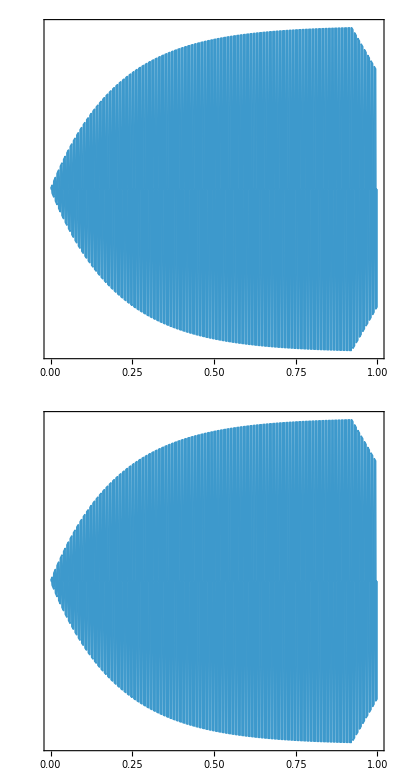

```mathematica
sr=44100; 
dur=1; 
samplesMono=Table[ADSR[t]*carre[t],{t,0,dur,1/sr}];
samplesMod=Table[ADSR[t]*carre[t],{t,0,dur,1/sr}];
yc=AudioChannelCombine[{Audio[samplesMono,SampleRate->sr],Audio[samplesMod,SampleRate->sr]}];
AudioPlot[yc]
yc2 =reverb[Sound[{Play[ADSR[t]*Fonction[t],{t,0,1.5}],Play[Sin[2π  432 t]*ADSR[t],{t,0,1.5}]}]]
```